Gaussian

```mathematica
$Assumptions={τ>0,τR>0,t>=0,τ-t>=0,u>=0,τ-u>=0};
```

```mathematica
Psi[t_]= Sinc[π t/(2τR)];
dPsi[t_]=D[Psi[t],t];
ddPsi[t_]=D[dPsi[t],t];
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi[t],t,s]);

c0=((-4+π^2) τR^2)/π^2;
```

```mathematica
g[t_]=(t+τR)/(τ+2τR);

gs[t_]=c0(DiracDelta[t]-DiracDelta[τ-t])/(τ+2τR);


h1[t_]=t/τ;
h2[t_]=t/τ+Sin[ π t/τ];
```

```mathematica
Wh1[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]h1[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h1[t]h1[u],{t,0,τ},{u,0,τ}];
```

```mathematica
Wh2[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]h2[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]h2[t]h2[u],{t,0,τ},{u,0,τ}]
```

$Aborted

```mathematica
(*data=List[];*)

τR=1;

(*data=Table[{τ,Psi[0]/2+NIntegrate[dPsi[τ-t]h2[t],{t,0,τ}]-1/2 NIntegrate[ddPsi[t-u]h2[t]h2[u],{t,0,τ},{u,0,τ}]},{τ,0.001,0.01-0.001/5,0.001/5}];*)

Do[

aux=Table[{τ,Psi[0]/2+NIntegrate[dPsi[τ-t]h2[t],{t,0,τ}]-1/2 NIntegrate[ddPsi[t-u]h2[t]h2[u],{t,0,τ},{u,0,τ}]},{τ,0.001*10^n+0.002*10^(n-1),0.001*10^(n+1),0.002*10^(n-1)}];

Do[

data=AppendTo[data,aux[[j]]];

,{j,1,45}];

,{n,4,4}];

Clear[τR]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.36429 and 3.4259×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.34539 and 1.45885×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.33415 and 2.07202×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
data
```

{{0.001,0.5},{0.0012,0.5},{0.0014,0.5},{0.0016,0.5},{0.0018,0.5},{0.002,0.500001},{0.0022,0.500001},{0.0024,0.500001},{0.0026,0.500001},{0.0028,0.500001},{0.003,0.500001},{0.0032,0.500001},{0.0034,0.500002},{0.0036,0.500002},{0.0038,0.500002},{0.004,0.500002},{0.0042,0.500002},{0.0044,0.500003},{0.0046,0.500003},{0.0048,0.500003},{0.005,0.500003},{0.0052,0.500004},{0.0054,0.500004},{0.0056,0.500004},{0.0058,0.500004},{0.006,0.500005},{0.0062,0.500005},{0.0064,0.500005},{0.0066,0.500006},{0.0068,0.500006},{0.007,0.500006},{0.0072,0.500007},{0.0074,0.500007},{0.0076,0.500008},{0.0078,0.500008},{0.008,0.500008},{0.0082,0.500009},{0.0084,0.500009},{0.0086,0.50001},{0.0088,0.50001},{0.009,0.500011},{0.0092,0.500011},{0.0094,0.500012},{0.0096,0.500012},{0.0098,0.500013},{0.012,0.500019},{0.014,0.500026},{0.016,0.500034},{0.018,0.500043},{0.02,0.500053},{0.022,0.500064},{0.024,0.500076},{0.026,0.500089},{0.028,0.500104},{0.03,0.500119},{0.032,0.500136},{0.034,0.500153},{0.036,0.500172},{0.038,0.500191},{0.04,0.500212},{0.042,0.500234},{0.044,0.500256},{0.046,0.50028},{0.048,0.500305},{0.05,0.500331},{0.052,0.500358},{0.054,0.500386},{0.056,0.500415},{0.058,0.500445},{0.06,0.500476},{0.062,0.500509},{0.064,0.500542},{0.066,0.500577},{0.068,0.500612},{0.07,0.500649},{0.072,0.500686},{0.074,0.500725},{0.076,0.500764},{0.078,0.500805},{0.08,0.500847},{0.082,0.50089},{0.084,0.500934},{0.086,0.500979},{0.088,0.501025},{0.09,0.501072},{0.092,0.50112},{0.094,0.501169},{0.096,0.501219},{0.098,0.501271},{0.1,0.501323},{0.012,0.500019},{0.014,0.500026},{0.016,0.500034},{0.018,0.500043},{0.02,0.500053},{0.022,0.500064},{0.024,0.500076},{0.026,0.500089},{0.028,0.500104},{0.03,0.500119},{0.032,0.500136},{0.034,0.500153},{0.036,0.500172},{0.038,0.500191},{0.04,0.500212},{0.042,0.500234},{0.044,0.500256},{0.046,0.50028},{0.048,0.500305},{0.05,0.500331},{0.052,0.500358},{0.054,0.500386},{0.056,0.500415},{0.058,0.500445},{0.06,0.500477},{0.062,0.500509},{0.064,0.500542},{0.066,0.500577},{0.068,0.500612},{0.07,0.500649},{0.072,0.500686},{0.074,0.500725},{0.076,0.500764},{0.078,0.500805},{0.08,0.500847},{0.082,0.50089},{0.084,0.500934},{0.086,0.500979},{0.088,0.501025},{0.09,0.501072},{0.092,0.50112},{0.094,0.501169},{0.096,0.501219},{0.098,0.501271},{0.1,0.501323},{0.12,0.501904},{0.14,0.502591},{0.16,0.503383},{0.18,0.504279},{0.2,0.50528},{0.22,0.506385},{0.24,0.507593},{0.26,0.508904},{0.28,0.510319},{0.3,0.511835},{0.32,0.513453},{0.34,0.515172},{0.36,0.516992},{0.38,0.518911},{0.4,0.520929},{0.42,0.523046},{0.44,0.52526},{0.46,0.527571},{0.48,0.529978},{0.5,0.53248},{0.52,0.535077},{0.54,0.537766},{0.56,0.540548},{0.58,0.543421},{0.6,0.546385},{0.62,0.549438},{0.64,0.552578},{0.66,0.555806},{0.68,0.55912},{0.7,0.562518},{0.72,0.566},{0.74,0.569564},{0.76,0.573209},{0.78,0.576933},{0.8,0.580736},{0.82,0.584616},{0.84,0.588571},{0.86,0.592601},{0.88,0.596703},{0.9,0.600877},{0.92,0.605121},{0.94,0.609433},{0.96,0.613812},{0.98,0.618256},{1.,0.622764},{1.2,0.670994},{1.4,0.723762},{1.6,0.779278},{1.8,0.83571},{2.,0.891248},{2.2,0.944182},{2.4,0.992962},{2.6,1.03625},{2.8,1.07298},{3.,1.10236},{3.2,1.12389},{3.4,1.1374},{3.6,1.14299},{3.8,1.14102},{4.,1.1321},{4.2,1.11699},{4.4,1.09662},{4.6,1.07198},{4.8,1.04412},{5.,1.01405},{5.2,0.982742},{5.4,0.951068},{5.6,0.919783},{5.8,0.889507},{6.,0.860708},{6.2,0.83371},{6.4,0.808695},{6.6,0.785716},{6.8,0.764718},{7.,0.745562},{7.2,0.728043},{7.4,0.71192},{7.6,0.696936},{7.8,0.682839},{8.,0.6694},{8.2,0.656422},{8.4,0.643751},{8.6,0.631279},{8.8,0.618944},{9.,0.606726},{9.2,0.59464},{9.4,0.582727},{9.6,0.571046},{9.8,0.559665},{10.,0.54865},{12.,0.463294},{14.,0.401237},{16.,0.353505},{18.,0.316041},{20.,0.285641},{22.,0.260629},{24.,0.239594},{26.,0.221728},{28.,0.206316},{30.,0.192922},{32.,0.181148},{34.,0.170736},{36.,0.161448},{38.,0.153125},{40.,0.145611},{42.,0.138805},{44.,0.132603},{46.,0.126934},{48.,0.121727},{50.,0.116933},{52.,0.1125},{54.,0.108392},{56.,0.104572},{58.,0.101014},{60.,0.0976886},{62.,0.0945761},{64.,0.091655},{66.,0.0889095},{68.,0.0863232},{70.,0.0838835},{72.,0.0815749},{74.,0.0793953},{76.,0.0773264},{78.,0.0753631},{80.,0.0734964},{82.,0.0717202},{84.,0.0700304},{86.,0.0684134},{88.,0.0668738},{90.,0.0653981},{92.,0.0639889},{94.,0.0626343},{96.,0.0613421},{98.,0.0601072},{100.,0.058911}}

```mathematica
W0[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]g[t]g[u],{t,0,τ},{u,0,τ}]
```

1/2-(8 τ τR^2-π^2 τ (τ^2+2 τ τR+2 τR^2)-8 τ τR^2 Cos[(π τ)/(2 τR)]+4 π τR^2 (τ+τR) Sin[(π τ)/(2 τR)])/(2 π^2 τ (τ+2 τR)^2)-(π (τ+τR)-(2 τR^2 Sin[(π τ)/(2 τR)])/τ-2 τR SinIntegral[(π τ)/(2 τR)])/(π (τ+2 τR))

```mathematica
W1[τ_]=W0[τ]+c0 dPsi[τ]/(τ+2τR)-c0/(τ+2τR)Integrate[ddPsi[t]g[t],{t,0,τ}]+c0/(τ+2τR)Integrate[ddPsi[τ-t]g[t],{t,0,τ}]-c0^2/(τ+2τR)^2 Limit[ddPsi[t],t->0]+c0^2/(τ+2τR)^2 ddPsi[τ]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2+((-4+π^2)^2 τR^2)/(12 π^2 (τ+2 τR)^2)+((-4+π^2) τR^2 (π τ (-τ+τR Cos[(π τ)/(2 τR)])+2 (τ-τR) τR Sin[(π τ)/(2 τR)]))/(π^3 τ^2 (τ+2 τR)^2)+((-4+π^2)^2 τR^3 (-(4 τR Cos[(π τ)/(2 τR)])/(π τ^2)-Sin[(π τ)/(2 τR)]/τ+(8 τR^2 Sin[(π τ)/(2 τR)])/(π^2 τ^3)))/(2 π^3 (τ+2 τR)^2)+((-4+π^2) τR ((2 τR Cos[(π τ)/(2 τR)])/(π τ)-(4 τR^2 Sin[(π τ)/(2 τR)])/(π^2 τ^2)))/(2 π (τ+2 τR))-(8 τ τR^2-π^2 τ (τ^2+2 τ τR+2 τR^2)-8 τ τR^2 Cos[(π τ)/(2 τR)]+4 π τR^2 (τ+τR) Sin[(π τ)/(2 τR)])/(2 π^2 τ (τ+2 τR)^2)-((-4+π^2) τR^2 (π τ^2+π τ (τ+τR) Cos[(π τ)/(2 τR)]-2 τR (2 τ+τR) Sin[(π τ)/(2 τR)]))/(π^3 τ^2 (τ+2 τR)^2)-(π (τ+τR)-(2 τR^2 Sin[(π τ)/(2 τR)])/τ-2 τR SinIntegral[(π τ)/(2 τR)])/(π (τ+2 τR))

```mathematica
Wh1[τ_]=-1/2+(π^2 τ^2-8 τR^2+8 τR^2 Cos[(π τ)/(2 τR)])/(2 π^2 τ^2)+(2 τR SinIntegral[(π τ)/(2 τR)])/(π τ);
```

```mathematica
data={{0.001,0.5000001323971994},{0.0012000000000000001,0.5000001906524563},{0.0014,0.5000002594983104},{0.0016,0.5000003389362225},{0.0018,0.5000004289674695},{0.002,0.5000005295888924},{0.0022,0.5000006408023246},{0.0024000000000000002,0.5000007626078934},{0.0026,0.5000008950046348},{0.0028000000000000004,0.5000010379935523},{0.003,0.5000011915741136},{0.0032,0.5000013557460896},{0.0034000000000000002,0.5000015305101794},{0.0036000000000000003,0.5000017158663156},{0.0038,0.5000019118141864},{0.004,0.5000021183527195},{0.004200000000000001,0.5000023354836913},{0.0044,0.500002563206394},{0.0046,0.5000028015205847},{0.0048000000000000004,0.5000030504269671},{0.005,0.5000033099248801},{0.005200000000000001,0.5000035800132829},{0.0054,0.5000038606945344},{0.0056,0.500004151966683},{0.0058000000000000005,0.5000044538308226},{0.006,0.5000047662865795},{0.006200000000000001,0.5000050893340441},{0.0064,0.5000054229726482},{0.0066,0.500005767202946},{0.0068000000000000005,0.5000061220253438},{0.007,0.5000064874393764},{0.007200000000000001,0.5000068634450299},{0.0074,0.5000072500411693},{0.0076,0.5000076472295848},{0.0078000000000000005,0.5000080550092852},{0.008,0.5000084733804825},{0.0082,0.5000089023433709},{0.008400000000000001,0.5000093418974462},{0.0086,0.500009792042474},{0.0088,0.5000102527800802},{0.009000000000000001,0.5000107241082786},{0.0092,0.5000112060283697},{0.009400000000000002,0.5000116985396712},{0.009600000000000001,0.500012201642524},{0.0098,0.5000127153359628},{0.012,0.5000190649871424},{0.014,0.5000259494331216},{0.016,0.50003389301321},{0.018000000000000002,0.500042895616954},{0.02,0.5000529572030185},{0.022,0.5000640778338858},{0.024,0.5000762574080448},{0.026000000000000002,0.5000894958738344},{0.028,0.5001037931023119},{0.030000000000000002,0.5001191492561647},{0.032,0.5001355641209158},{0.034,0.5001530376502749},{0.036000000000000004,0.5001715698438034},{0.038000000000000006,0.5001911605519436},{0.04,0.5002118096323335},{0.041999999999999996,0.5002335172763286},{0.044,0.5002562832245939},{0.046,0.5002801074318518},{0.048,0.5003049898041682},{0.05,0.5003309302122745},{0.052000000000000005,0.5003579286352388},{0.054000000000000006,0.5003859848986605},{0.055999999999999994,0.500415098698041},{0.057999999999999996,0.5004452705069049},{0.06,0.5004764998465768},{0.062,0.5005087865987066},{0.064,0.5005421307066525},{0.066,0.50057653201792},{0.068,0.5006119903822043},{0.07,0.5006485057293854},{0.072,0.5006860779131765},{0.074,0.5007247067533293},{0.076,0.5007643921803782},{0.078,0.5008051334171301},{0.08,0.5008469315941295},{0.082,0.5008897858329492},{0.084,0.5009336960279405},{0.086,0.5009786619896677},{0.088,0.5010246835788278},{0.09,0.5010717606233599},{0.092,0.501119892946525},{0.094,0.5011690804355063},{0.096,0.5012193228238779},{0.098,0.5012706199366601},{0.09999999999999999,0.5013229716682945},{0.12000000000000001,0.5019044485484843},{0.14,0.5025911487788677},{0.16,0.5033828250856909},{0.18,0.5042791908521417},{0.2,0.5052799216331919},{0.22000000000000003,0.5063846552942419},{0.24,0.5075929921747637},{0.26,0.5089044952609765},{0.28,0.5103186903840691},{0.3,0.5118350664257801},{0.32,0.5134530755478647},{0.34,0.5151721334284107},{0.36,0.516991619525647},{0.38,0.5189108773507758},{0.4,0.5209292147527276},{0.42,0.5230459042344429},{0.44,0.5252601833636463},{0.46,0.5275712547463561},{0.48,0.5299782866739366},{0.5,0.5324804139307372},{0.52,0.5350767372154752},{0.54,0.5377663241624688},{0.56,0.5405482096327189},{0.5800000000000001,0.5434213960982659},{0.6,0.5463848541043844},{0.62,0.5494375227140575},{0.64,0.5525783099746622},{0.66,0.5558060933938139},{0.68,0.5591197204615802},{0.7,0.5625180090378252},{0.72,0.5659997480741115},{0.74,0.5695636978877074},{0.76,0.5732085909125775},{0.78,0.5769331322192063},{0.8,0.5807359999255501},{0.8200000000000001,0.5846158459949563},{0.84,0.5885712966166481},{0.86,0.5926009529598277},{0.88,0.5967033916361999},{0.9,0.6008771653705238},{0.92,0.6051208038011613},{0.9400000000000001,0.6094328137234566},{0.96,0.6138116802338276},{0.98,0.6182558668363798},{1.,0.6227638165558187},{1.2,0.670994334708582},{1.4,0.7237616757884269},{1.6,0.7792784547824243},{1.8,0.8357098612309466},{2.,0.8912477999260531},{2.2,0.9441815397976536},{2.4000000000000004,0.9929615930271318},{2.6,1.036253988076282},{2.8,1.0729826801410047},{3.,1.1023585397051863},{3.2,1.1238940443264387},{3.4000000000000004,1.1374037972416486},{3.6000000000000005,1.1429913219372463},{3.8,1.1410237853624379},{4.,1.1320964009455203},{4.2,1.1169890090710484},{4.4,1.0966174633776062},{4.6000000000000005,1.0719826488056718},{4.8,1.0441198301604877},{5.,1.014050970276544},{5.2,0.9827421264198135},{5.4,0.9510677779215315},{5.6000000000000005,0.919783348040585},{5.800000000000001,0.889506611048102},{6.000000000000001,0.8607081074357834},{6.2,0.8337104060898901},{6.4,0.8086949746643977},{6.6000000000000005,0.7857158662161283},{6.800000000000001,0.7647184606034778},{7.000000000000001,0.7455618521064138},{7.2,0.7280427190081833},{7.4,0.7119196049088004},{7.6000000000000005,0.696935736154485},{7.800000000000001,0.6828392518100634},{8.,0.66939991766624},{8.2,0.6564216447238114},{8.4,0.6437506047776222},{8.6,0.6312789051880101},{8.8,0.6189442918902988},{9.,0.6067263104647647},{9.2,0.5946398264084891},{9.4,0.582726548138268},{9.6,0.5710457471777048},{9.799999999999999,0.5596647613003058},{10.,0.5486502022862512},{12.,0.4632937753201689},{14.,0.40123650870375993},{16.,0.3535052006001641},{18.,0.31604078892252074},{20.,0.2856408252572614},{22.,0.2606288069721766},{24.,0.2395940289862729},{26.,0.22172796147568352},{28.,0.20631598292547737},{30.,0.19292240615194312},{32.,0.18114751059406586},{34.,0.17073640536850954},{36.,0.16144835673942892},{38.,0.15312453599907905},{40.,0.14561142923498538},{42.,0.1388049955091084},{44.,0.13260277680947596},{46.,0.12693381440690799},{48.,0.12172713179820538},{50.,0.11693269067082412},{52.,0.11249977720931403},{54.,0.10839210486393802},{56.,0.10457247296207339},{58.,0.1010139527938908},{60.,0.09768863215251533},{62.,0.09457607582967642},{64.,0.09165496533076423},{66.,0.08890951557360083},{68.,0.08632317447292115},{70.,0.0838835029496281},{72.,0.08157487269618002},{74.,0.07939525409710213},{76.,0.07732639542380548},{78.,0.07536307320053304},{80.,0.07349643200916012},{82.,0.07172021055856792},{84.,0.07003039798977995},{86.,0.06841339529952761},{88.,0.06687375092369385},{90.,0.06539806359304368},{92.,0.06398891899327841},{94.,0.0626343143414726},{96.,0.06134211802289724},{98.,0.0601071918697621},{100.,0.05891101028052603}};

Wh2=Interpolation[data]
```

InterpolatingFunction[…]

```mathematica
W0[τ_]=1/2-(8 τ τR^2-π^2 τ (τ^2+2 τ τR+2 τR^2)-8 τ τR^2 Cos[(π τ)/(2 τR)]+4 π τR^2 (τ+τR) Sin[(π τ)/(2 τR)])/(2 π^2 τ (τ+2 τR)^2)-(π (τ+τR)-(2 τR^2 Sin[(π τ)/(2 τR)])/τ-2 τR SinIntegral[(π τ)/(2 τR)])/(π (τ+2 τR));
```

```mathematica
W1[τ_]=1/2+((-4+π^2)^2 τR^2)/(12 π^2 (τ+2 τR)^2)+((-4+π^2) τR^2 (π τ (-τ+τR Cos[(π τ)/(2 τR)])+2 (τ-τR) τR Sin[(π τ)/(2 τR)]))/(π^3 τ^2 (τ+2 τR)^2)+((-4+π^2)^2 τR^3 (-(4 τR Cos[(π τ)/(2 τR)])/(π τ^2)-Sin[(π τ)/(2 τR)]/τ+(8 τR^2 Sin[(π τ)/(2 τR)])/(π^2 τ^3)))/(2 π^3 (τ+2 τR)^2)+((-4+π^2) τR ((2 τR Cos[(π τ)/(2 τR)])/(π τ)-(4 τR^2 Sin[(π τ)/(2 τR)])/(π^2 τ^2)))/(2 π (τ+2 τR))-(8 τ τR^2-π^2 τ (τ^2+2 τ τR+2 τR^2)-8 τ τR^2 Cos[(π τ)/(2 τR)]+4 π τR^2 (τ+τR) Sin[(π τ)/(2 τR)])/(2 π^2 τ (τ+2 τR)^2)-((-4+π^2) τR^2 (π τ^2+π τ (τ+τR) Cos[(π τ)/(2 τR)]-2 τR (2 τ+τR) Sin[(π τ)/(2 τR)]))/(π^3 τ^2 (τ+2 τR)^2)-(π (τ+τR)-(2 τR^2 Sin[(π τ)/(2 τR)])/τ-2 τR SinIntegral[(π τ)/(2 τR)])/(π (τ+2 τR));
```

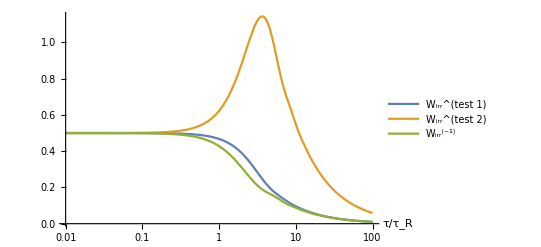

```mathematica
τR=1;
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test 1)"],Legended[Wh2[τ],"W_irr^(test 2)"],Legended[W0[τ],"W_irr^(-1)"]},{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR]
```

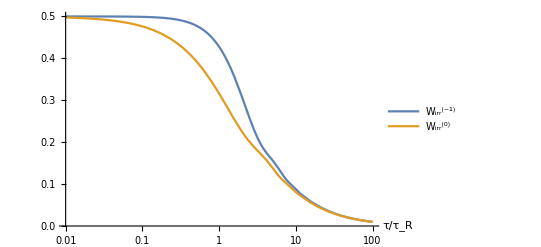

```mathematica
τR=1;
LogLinearPlot[{Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}]]
Clear[τR]
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

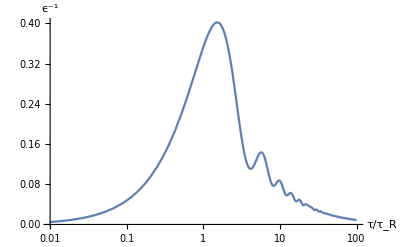

```mathematica
τR=1;
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^-1"}]
Clear[τR]
```

```mathematica
τR=1;

data=Table[{τ,ϵ1[τ]},{τ,0.001,0.01,0.001/100}];

Do[

aux=Table[{τ,ϵ1[τ]},{τ,0.001*10^n,0.001*10^(n+1),0.001*10^(n-1)}];

Do[

data=AppendTo[data,aux[[j]]];

,{j,1,91}];

,{n,1,4}];

Export["/home/pnaze/Research/ongoing/PNOP/data/data_abs_psi4.dat",data];

Clear[τR]
```